```mathematica
r=r0=2;μ=μ0=1;s=0.02;K=4 10^6;U=1 10^-6.;maxtime=5 10^6.;timebetweenenvchanges=x=70; initmostfitclass=40;
isubs=(r-μ)/(2s);
Print["successional if << 1: ", K(r-μ-i s)/r (μ+i s) U i Log[ K(r-μ-i s)/r s]/.i-> isubs];
Print["steady state q heuristic: ", 2 Log[ K(r-μ-i s) s/r]/Log[s/(U i)]/.i-> isubs];
Print["extinction threshold: i_ext=", Ceiling[(r-μ)/s]];
Print["Typical successional adaptation timescale: ", 1/( K/r(r-μ-i s)U i s) /.i-> isubs]
Print["Typical MM adaptation timescale: ", ((2Log[ K/r(r-i s-μ) s]-Log[s/(U i)])s/(Log[s/(U i)])^2)^-1 /.i-> isubs]
Print["Typical pop. size: ", K/r(r-μ-i s)/.i-> isubs]
verbose=False;
veryverbose=False;
```

successional if << 1: 371.381

steady state q heuristic: 2.96307

extinction threshold: i_ext=50

Typical successional adaptation timescale: 2.

Typical MM adaptation timescale: 170.259

Typical pop. size: 1.×10^6

```mathematica
(*Single runs*)
out=RunSimulationCheckEachMutation2[r,μ,s,K,U,1 10^5,150,20];
```

going extinct at time 45438.4 before time 45517.3 and 303 changes at rate 150

```mathematica
(*Scans over T, parallelized*)
With[{r=2,μ=1,s=0.02,K=4 10^6,U=1 10^-6.,maxtime=1 10^6.,initmostfitclass=20},
{extime,extinctiontimes}=AbsoluteTiming[ParallelTable[{x,RunSimulationCheckEachMutation2[r,μ,s,K,U,maxtime,x,initmostfitclass]},{x,180.5,190,0.5},Method->"FinestGrained"]]];
```

```mathematica
(*Multiple runs at one T, parallelized*)
With[{r=2,μ=1,s=0.02,K=4 10^6,U=1 10^-6.,maxtime=2 10^6.,initmostfitclass=20},
{extime,extinctiontimes}=AbsoluteTiming[ParallelTable[RunSimulationCheckEachMutation2[r,μ,s,K,U,maxtime,180,initmostfitclass],100,Method->"FinestGrained"]]];
```

```mathematica
extinctiontimesclean=Select[extinctiontimes,#[[1]]<2.*10^6&&#[[1]]>60000&];
Length[extinctiontimesclean]
exttimepositions=Ceiling[extinctiontimesclean[[All,1]]];
extinctiontimesclean=Table[extinctiontimesclean[[i]][[2]][[exttimepositions[[i]]-60000;;exttimepositions[[i]]]],{i,1,Length[extinctiontimesclean]}];
```

90

```mathematica
Export["/home/jbertram/repos/popgenextinction/code/test.csv",extinctiontimesclean];
```

```mathematica
(*Markov chain simulation; multiple mutations*)
(*Memoryless*)
timebetweenenvchanges=180;
M=Floor[(r-μ)/s]+1;
lambdas=Table[1/timebetweenenvchanges,{i,0,M-1}];
mus=Prepend[Table[( 2Log[ K/r(r-μ-i s)s]-Log[ s/(U i)])s/(Log[s/(U i)])^2,{i,1,M-1}],0];
A=ConstantArray[0,{M,M}];
For[i=2,i≤  M-1,i++,
A[[i]][[i-1]]=mus[[i]];
A[[i]][[i]]=1-lambdas[[i]]-mus[[i]];
A[[i]][[i+1]]=lambdas[[i]]];
A[[1]][[1]]=1-lambdas[[1]]; A[[1]][[2]]=lambdas[[1]];  
A[[M]][[M]]=1;
```

```mathematica
CMFmatrix=ConstantArray[0,{M,M}];
For[i=1,i≤M,i++,CMFmatrix[[i]]=Accumulate[A[[i]]]]
simulatetransittime[]:=Module[{rand,state,states},
state=40;i=1;
While[state<M && i<2000000,
rand=RandomReal[];
If[rand>CMFmatrix[[state]][[state]],state=state+1,
If[rand<CMFmatrix[[state]][[state-1]],state=state-1]
];
i++
];
i
];
```

{21034.8,Null}

100000

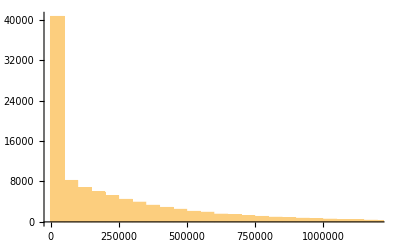

```mathematica
timesdirect=ParallelTable[simulatetransittime[],{100000}];//AbsoluteTiming
Print[Length[timesdirect]]
Histogram[timesdirect]
(*Print[Mean[timesdirect]//N];*)
```

```mathematica
Export["/home/jbertram/repos/popgenextinction/code/tehist.csv",timesdirect,"Data"]
```

/home/jbertram/repos/popgenextinction/code/tehist.csv

```mathematica
Mean[timesdirect]//N
```

239033.

```mathematica
exttimeunitstepmm[180,20,U,s,K,1]
```

362875.